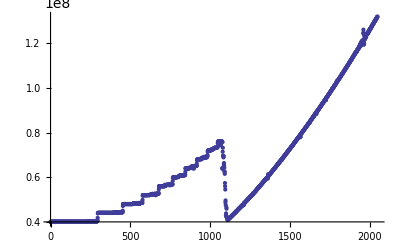

```mathematica
data :=Import["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-bag.csv", "Table", {"FieldSeparators" -> ";"}]
cols :=data[[All,{1,4}]]
ListPlot[cols]
```

```mathematica
f[x_]:= Piecewise[{{a,x<xa},{a+(b-a)(x-xa)/(xb-xa),xa≤x<xb},{b,xb≤x}}]
fit = NonlinearModelFit[cols,f[x],{a,b,{xa,100},{xb,200}},x]
Show[ListPlot[data],Plot[fit[x],{x,0,2048},PlotStyle->{Red,Thick}]]
```

FittedModel[Piecewise[{{1022.63, x<-407.154}, {1022.63+693866. (407.154+x), «1»}, {«22», «1»}, {0, «1»}}]]

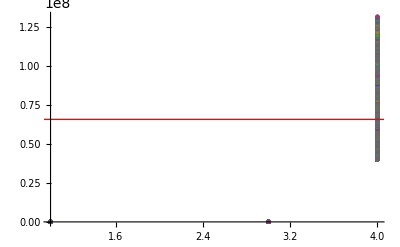
```mathematica
-Graphics-
nlm = NonlinearModelFit[cols,Piecewise[{{a,x<A},{b,x>B}}],{a,b,A,B,c,d},x]
```

-Graphics-

FittedModel[Piecewise[{{3.99974×10^7, x<1.}, {6.58897×10^7, x>1.}, {0, True}}]]